```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
data = {{0,0.12,0,0.02},{16,0.42,0,0.02},{32,0.74,0,0.02},{48,1.06,0,0.02},{64,1.38,0,0.02},{80,1.7,0,0.02},{96,2,0,0.02},{112,2.3,0,0.02},{128,2.64,0,0.02},{144,2.92,0,0.02},{160,3.24,0,0.02},{176,3.58,0,0.02},{192,3.9,0,0.02},{208,4.2,0,0.02},{224,4.54,0,0.02},{240,4.84,0,0.02}}
```

{{0,0.12,0,0.02},{16,0.42,0,0.02},{32,0.74,0,0.02},{48,1.06,0,0.02},{64,1.38,0,0.02},{80,1.7,0,0.02},{96,2,0,0.02},{112,2.3,0,0.02},{128,2.64,0,0.02},{144,2.92,0,0.02},{160,3.24,0,0.02},{176,3.58,0,0.02},{192,3.9,0,0.02},{208,4.2,0,0.02},{224,4.54,0,0.02},{240,4.84,0,0.02}}

```mathematica
rdata:={#1,#2} &@@@data
```

```mathematica
lm=LinearModelFit[rdata,x,x]
```

FittedModel[0.111471+0.0196857 x]

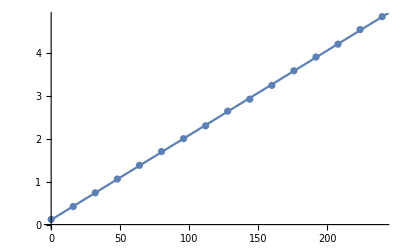

```mathematica
Show[ErrorListPlot[{{#1,#2},ErrorBarPlots`ErrorBar@@{#3,#4}}&@@@data,PlotRangePadding->{Automatic}],Plot[lm[x],{x,0,300}]]
```

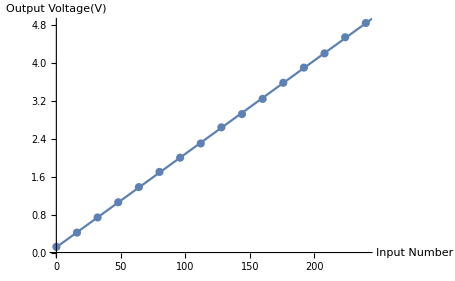

```mathematica
Show[%10,AxesLabel->{HoldForm[Input Number],HoldForm[Output Voltage[V]]},PlotLabel->None,LabelStyle->{FontFamily->"Garamond Premier Pro",12,GrayLevel[0]}]
```

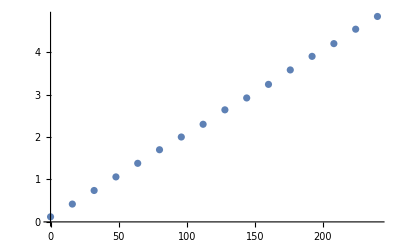

```mathematica
ErrorListPlot[{{#1,#2},ErrorBarPlots`ErrorBar@@{#3,#4}}&@@@data,PlotRangePadding->{Automatic}]
```

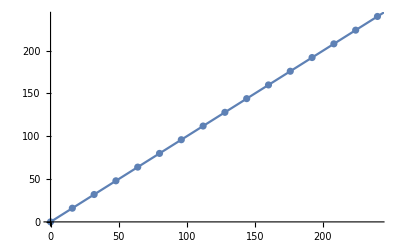

```mathematica
Show[ListPlot[Table[{x,x},{x,0,255,16}],PlotRangePadding->{Automatic}],Plot[x,{x,0,300}]]
```

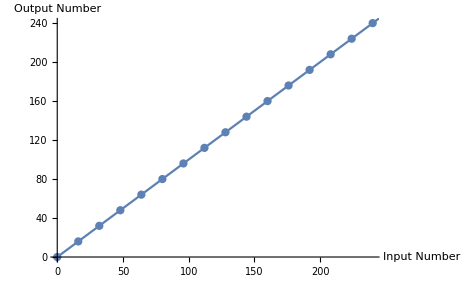

```mathematica
Show[%15,AxesLabel->{HoldForm[Input Number],HoldForm[Output Number]},PlotLabel->None,LabelStyle->{FontFamily->"Garamond Premier Pro",12,GrayLevel[0]}]
```